# Report Project 2

Course code: IX1501
Date: 2019-09-08

Viktor Jäger, vjager@kth.se
Sam Florin, sflorin@kth.se

Task: Distributions II

## Summery

### Task

Which distribution?
In this task, randomNumber[i, n] can be used to generate data for the distributions i=1,2,…,6. They are all distributions that are mentioned in the course literature (Blom Sec. 3.4 and Sec. 3.6). Do the following assignments for each of six distributions, i.e. i∈{1,2,…,6}. 

	* Use the straight line approach to determine a distribution model.
	* Determine point estimates of the parameters.
	* Compute 95% confidence intervals for the parameters. The interval should not be longer than 10% of its mean, 		   e.g. μ (1±0.05).

### Result

##### Straight Line Approach

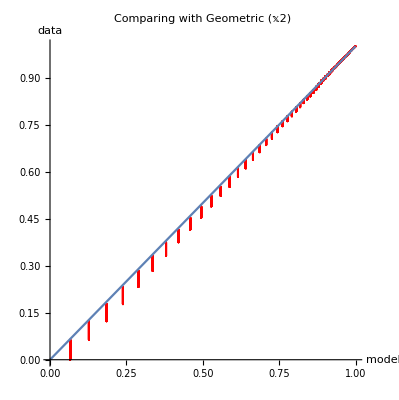

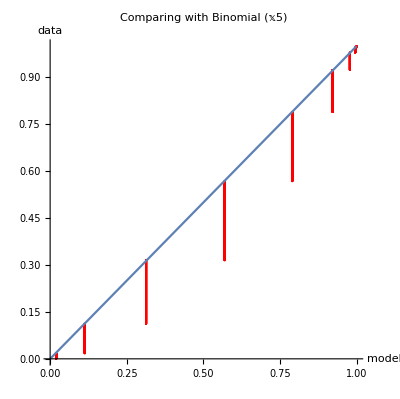

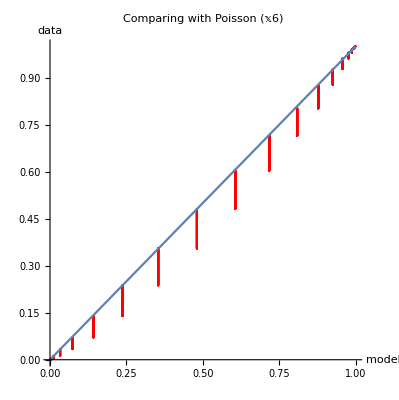

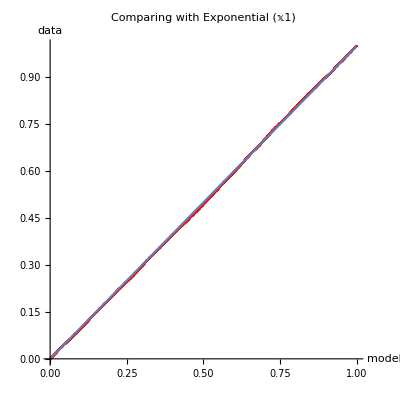

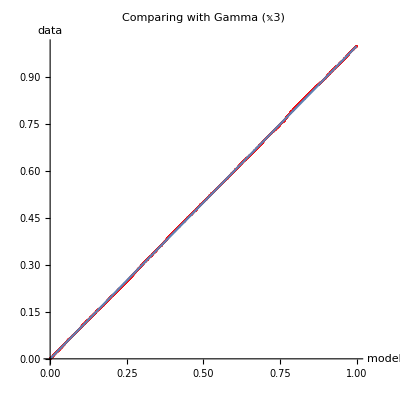

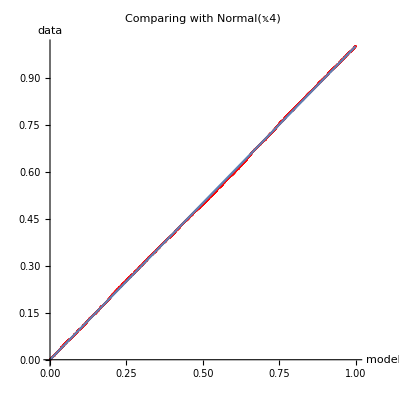

##### Point Estimation

X_1∈Exp(λ)
expectedValue = Mean[𝕩1];
λ = 1/expectedValue
λ=4.51984

X_2∈Ge(𝓅)
expectedValue = Mean[𝕩2] // N;
p = 1/expectedValue
0.0705945

X_3∈Γ(α,β) 
µ=Mean[𝕩3];
σ=StandardDeviation[𝕩3];
Solve[{α==µ/β, β==(σ^2)/(µ)},{α,β}]
α=7.89637
β=1.617716

X_4∈N(μ,σ) 
μ = Mean[𝕩4]
σ = StandardDeviation[𝕩4]
μ = 3.05929
σ = 4.97855

X_5∈Bin(𝓃,𝓅)
expectedValue = Mean[𝕩5];
standardDeviation = StandardDeviation[𝕩5];
Solve[{expectedValue == n*p, standardDeviation^2 == n*p*(1 - p)}, {n, p}] // N
n = 10.7759
p = 0.306118

X_6∈Po(μ) 
μ = Mean[𝕩6] // N
μ = 9.8184

##### Confidence Interval

X_1∈Exp(λ)
λ-Confidence Interval: (4.41833, 4.65819)

X_2∈Ge(𝓅)
p-Confidence Interval: (0.0654853, 0.0692719)

X_3 Γ(α,β)
α-Confidence Interval: (7.84869, 8.47811)
β-Confidence Interval: (1.531071, 1.650756)

X_4∈N(μ,σ)
μ-Confidence Interval: (2.79686, 3.10669)
σ-Confidence Interval: (4.80497, 5.00104)

X_5∈Bin(𝓃,𝓅)
n-Confidence Interval: (9.76374, 12.6763)
p-Confidence Interval: (0.302882 ,0.353284)

X_6∈Po(μ) 
μ-Confidence Interval: (9.73464, 9.91016)

## Discussion

### Straight Line Approach

An approach is simply to use the model function directly. We don’t have to worry about inverse function. This means that we are comparing y-axes. This is particularly useful in the cdf case since the output (or y-values) is always in the interval [0,1].
We are now going to compare the previous data to a presumed model. We start the examination by computing estimates of the expectation value and the standard deviation. 
x̄=1/n∑_(i=1)^n x_i, s=√(1/(n-1)∑_(i=1)^n (x_i-x̄)^2)

Check the data against the model cdf. If it fits it' s most likely the correct distribution.

### Point Estimation

When the sample size increases, the accuracy of the point estimate parameters gets better.

Distribution 𝕩1: Parameter λ can be estimated by using the arithmetic mean of the distribution,λ=1/(Χ̄) 

Distribution 𝕩2: Parameter 𝓅 can be estimated by using the arithmetic mean of the distribution, 𝓅=1/(Χ̄) 

Distribution 𝕩3: Parameters α, β are estimated by the formulas, μ=α·β and σ^2=μ·β

Distribution 𝕩4: Sats 6.2 Blom: If X ∈ N(μ,σ) the following applies: E(X)=μ,   V(X)=σ^2,   D(X)=σ 

Distribution 𝕩5: Sats 7.2 Blom: If X ∈ Bin(n,p) the following applies: 
	E(X)=np,   V(X)=np(1-p),   D(X)=√(np(1-p)) 

Distribution 𝕩6: Sats 7.7 Blom: If X ∈ Po(μ) the following applies: 
	E(X)=μ,   V(X)=μ,   D(X)=√μ

### Confidence Interval

We generate a list of many samples and calculate the estimated sample parameter for each of the samples. Then we calculate the confidence interval of 95% for the population mean estimated from these. We make sure that the length of the confidence interval is smaller than 10% of the arithmetic mean of the sample to meet the final condition in the task.

By generating a list of many samples the accuracy of the estimated confidence interval gets better.

When X_i∉𝒩(μ,σ) the given confidence intervals are approximate and We need to ensure large enough sample size.
The needed size is dependent on the distribution of X_i. If X_i have a symmetric distribution and iid (independent identical distributed) it’s often enough with a sample size of 20.

## Code

Straight Line Approach

#### Setup and Graph

```mathematica
SetDirectory[NotebookDirectory[]];
Once[Get["Project2.m","IX1501"]];
```

```mathematica
(* declare and generate the 6 unknown distributions *)
(* sort and plot the n points of the distributions *)
n=10000;
𝕩1=randomNumber[1,n];
𝕩2=randomNumber[2,n];
𝕩3=randomNumber[3,n];
𝕩4=randomNumber[4,n];
𝕩5=randomNumber[5,n];
𝕩6=randomNumber[6,n];

𝕩1sort=Sort[𝕩1];
𝕩2sort=Sort[𝕩2];
𝕩3sort=Sort[𝕩3];
𝕩4sort=Sort[𝕩4];
𝕩5sort=Sort[𝕩5];
𝕩6sort=Sort[𝕩6];
```

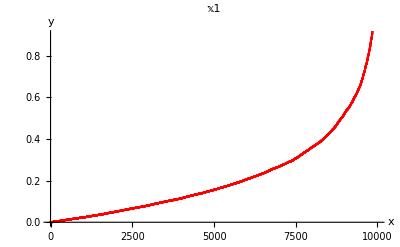

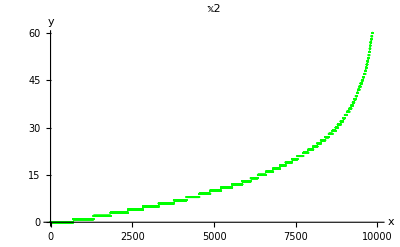

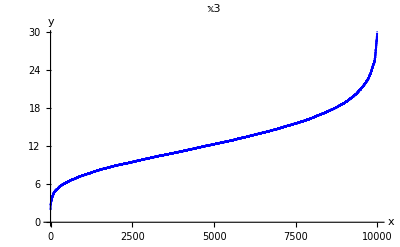

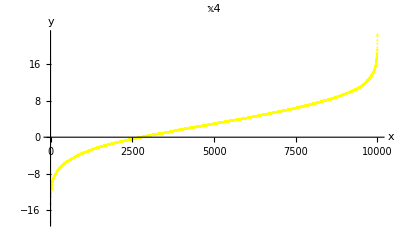

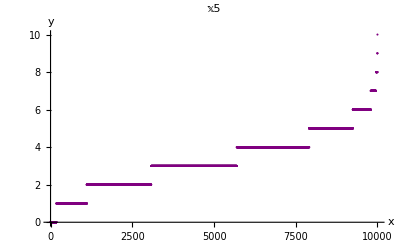

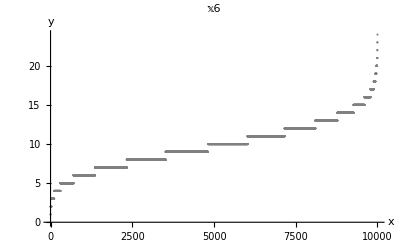

```mathematica
ListPlot[𝕩1sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Red,PlotLabel->"𝕩1"]
ListPlot[𝕩2sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Green,PlotLabel->"𝕩2"]
ListPlot[𝕩3sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Blue,PlotLabel->"𝕩3"]
ListPlot[𝕩4sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Yellow,PlotLabel->"𝕩4"]
ListPlot[𝕩5sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Purple,PlotLabel->"𝕩5"]
ListPlot[𝕩6sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Gray,PlotLabel->"𝕩6"]

(* Below: Plot all the unknown functions in sorted form *)
```

```mathematica
(* 
Let each value correspond to and increase of Δ=1/n probability. Also let each value correspond to the mid point in the Δinterval so the first value Subscript[x, 1] corresponds to P(X≤Subscript[x, 1])=Δ/2 and the value Subscript[x, k] to P(X≤Subscript[x, k])=Δ/2+(k-1) Δ. 
*)
```

```mathematica
Δ=1/n;
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
(* lineplot to be used to compare the data to the model, declared "globally" here *)
lineplot=Plot[x,{x,0,1}];
```

```mathematica
𝕩1𝕡data=Transpose[{𝕩1sort,𝕡data}];
𝕩2𝕡data=Transpose[{𝕩2sort,𝕡data}];
𝕩3𝕡data=Transpose[{𝕩3sort,𝕡data}];
𝕩4𝕡data=Transpose[{𝕩4sort,𝕡data}];
𝕩5𝕡data=Transpose[{𝕩5sort,𝕡data}];
𝕩6𝕡data=Transpose[{𝕩6sort,𝕡data}];
```

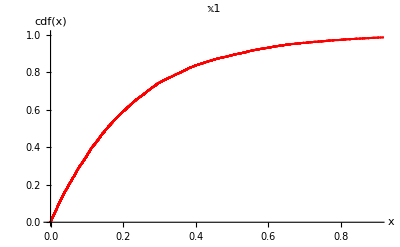

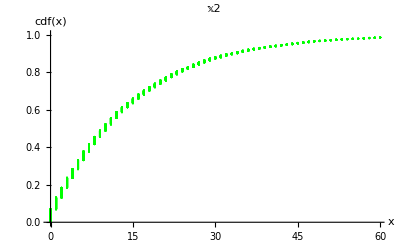

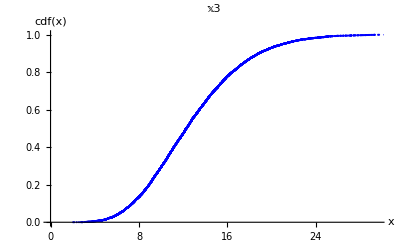

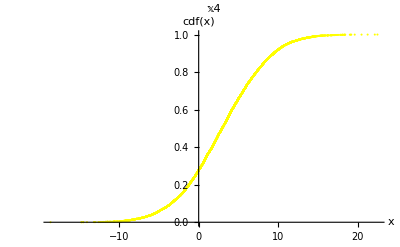

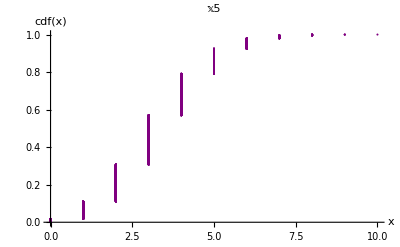

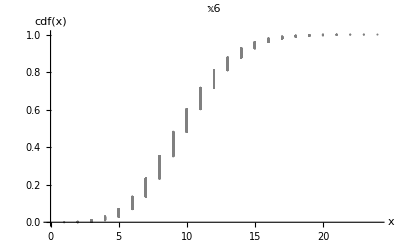

```mathematica
ListPlot[𝕩1𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Red,PlotLabel->"𝕩1"]
ListPlot[𝕩2𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Green,PlotLabel->"𝕩2"]
ListPlot[𝕩3𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Blue,PlotLabel->"𝕩3"]
ListPlot[𝕩4𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Yellow,PlotLabel->"𝕩4"]
ListPlot[𝕩5𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Purple,PlotLabel->"𝕩5"]
ListPlot[𝕩6𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Gray,PlotLabel->"𝕩6"]
```

#### Discrete Distribution (𝕩2, 𝕩5, 𝕩6)

##### Distribution 𝕩2

```mathematica
(* 𝕩2 : Geometric distribution model-data setup *)
Clear[p];
𝒢GeoDist𝕩2=EstimatedDistribution[𝕩2,GeometricDistribution[p]]
𝕡modelGeoDist𝕩2=CDF[𝒢GeoDist𝕩2,𝕩2sort];
comparedataGeoDist𝕩2=Transpose[{𝕡modelGeoDist𝕩2,𝕡data}];
dataplotGeoDist𝕩2=ListPlot[comparedataGeoDist𝕩2,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Geometric (𝕩2)",AspectRatio->Automatic];
```

GeometricDistribution[0.0654527]

##### Distribution 𝕩5

```mathematica
(* 𝕩5 : Binomial distribution model-data setup *)
Clear[n,p];
𝒢BinDist𝕩5=EstimatedDistribution[𝕩5,BinomialDistribution[n,p]];
𝕡modelBinDist𝕩5=CDF[𝒢BinDist𝕩5,𝕩5sort];
comparedataBinDist𝕩5=Transpose[{𝕡modelBinDist𝕩5,𝕡data}];
dataplotBinDist𝕩5=ListPlot[comparedataBinDist𝕩5,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Binomial (𝕩5)",AspectRatio->Automatic];
```

##### Distribution 𝕩6

```mathematica
(* 𝕩6 : Poisson distribution model-data setup *)
Clear[μ];
𝒢PoDist𝕩6=EstimatedDistribution[𝕩6,PoissonDistribution[μ]];
𝕡modelPoDist𝕩6=CDF[𝒢PoDist𝕩6,𝕩6sort];
comparedataPoDist𝕩6=Transpose[{𝕡modelPoDist𝕩6,𝕡data}];
dataplotPoDist𝕩6=ListPlot[comparedataPoDist𝕩6,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Poisson (𝕩6)",AspectRatio->Automatic];
```

#### Continuous Distribution (𝕩1, 𝕩3, 𝕩4)

##### Distribution 𝕩1

```mathematica
(* 𝕩1 : Exponential distribution model-data setup *)
c=30;
𝒢ExpDist𝕩1=EstimatedDistribution[𝕩1,ExponentialDistribution[c*λ]];
𝕡modelExpDist𝕩1=CDF[𝒢ExpDist𝕩1,𝕩1sort];
comparedataExpDist𝕩1=Transpose[{𝕡modelExpDist𝕩1,𝕡data}];
dataplotExpDist𝕩1=ListPlot[comparedataExpDist𝕩1,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Exponential (𝕩1)",AspectRatio->Automatic];
```

##### Distribution 𝕩3

```mathematica
(* 𝕩3 : Gamma distribution model-data setup *)
Clear[α,β];
𝒢GammaDist𝕩3=EstimatedDistribution[𝕩3,GammaDistribution[α,β]];
𝕡modelGammaDist𝕩3=CDF[𝒢GammaDist𝕩3,𝕩3sort];
comparedataGammaDist𝕩3=Transpose[{𝕡modelGammaDist𝕩3,𝕡data}];
dataplotGammaDist𝕩3=ListPlot[comparedataGammaDist𝕩3,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Gamma (𝕩3)",AspectRatio->Automatic];
```

##### Distribution 𝕩4

```mathematica
(* 𝕩4 : Normal distribution model-data setup *)
x4=Mean[𝕩4];
s4=StandardDeviation[𝕩4];
𝒩4=NormalDistribution[x4,s4];
𝕡modelNormalDist𝕩4=CDF[𝒩4,𝕩4sort];
comparedataNormalDist𝕩4=Transpose[{𝕡modelNormalDist𝕩4,𝕡data}];
dataplotNormalDist𝕩4=ListPlot[comparedataNormalDist𝕩4,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Normal(𝕩4)",AspectRatio->Automatic];
```

#### Display Graphs

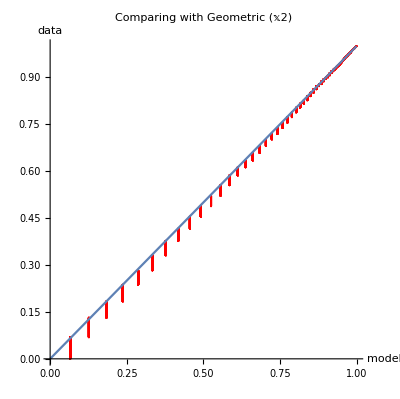

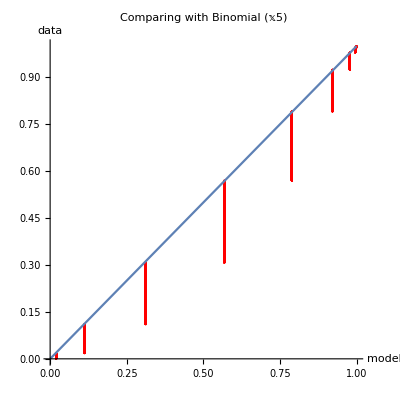

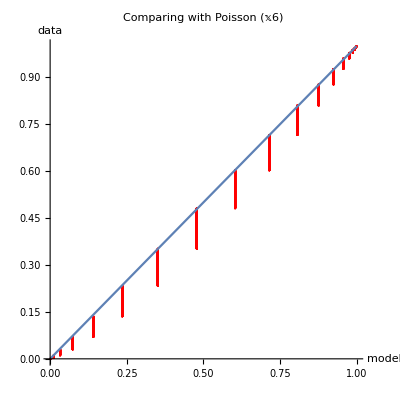

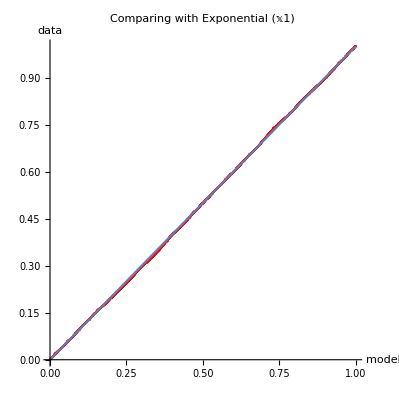

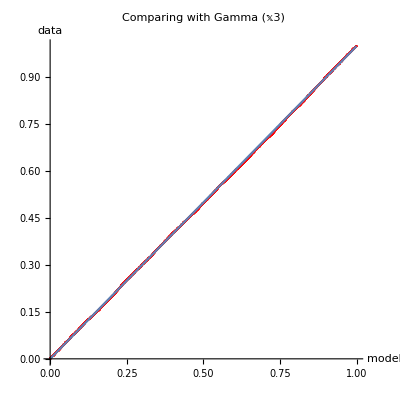

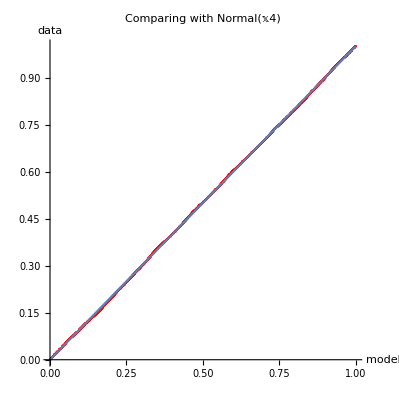

```mathematica
Show[dataplotGeoDist𝕩2, lineplot] 
Show[dataplotBinDist𝕩5, lineplot] 
Show[dataplotPoDist𝕩6, lineplot] 
Show[dataplotExpDist𝕩1, lineplot] 
Show[dataplotGammaDist𝕩3,lineplot]
Show[dataplotNormalDist𝕩4,lineplot]
```

Point Estimate

#### Setup

```mathematica
(* Import library *)
Needs["HypothesisTesting`"]
```

#### Distribution 𝕩1

```mathematica
(* Parameter λ can be estimated by using the arithmetic mean of the distribution,
	λ=1/(Χ̄) 
*)
```

```mathematica
Clear[λ];
FindDistributionParameters[𝕩1,ExponentialDistribution[λ]]
expectedValue=Mean[𝕩1];
λ=1/expectedValue
```

{λ→4.46002}

4.46002

#### Distribution 𝕩2

```mathematica
(* Parameter 𝓅 can be estimated by using the arithmetic mean of the distribution, 
	𝓅=1/(Χ̄) 
*)
```

```mathematica
Clear[p,expectedValue];
FindDistributionParameters[𝕩2,GeometricDistribution[p]]
standardDeviation=StandardDeviation[𝕩2];
expectedValue=Mean[𝕩2] //N;
p=1/expectedValue
p=√(1+4*standardDeviation^2)/(2*standardDeviation^2) //N
```

{p→0.0654527}

0.0700368

0.0678655

#### Distribution 𝕩3

```mathematica
Clear[α,β];
FindDistributionParameters[𝕩3,GammaDistribution[α,β]]
µ=Mean[𝕩3];
σ=StandardDeviation[𝕩3];
Solve[{α==µ/β, β==(σ^2)/(µ)},{α,β}]
```

{α→7.88619,β→1.62394}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→7.96455,β→1.60796}}

#### Distribution 𝕩4

```mathematica
(* Sats 6.2 Blom: If X ∈ N(μ,σ) the following applies: 
	E(X)=μ,   V(X)=σ^2,   D(X)=σ 
*)
```

```mathematica
Clear[μ,σ];
FindDistributionParameters[𝕩4,NormalDistribution[μ,σ]]
μ=Mean[𝕩4]
σ=StandardDeviation[𝕩4]
```

{μ→2.96692,σ→5.03847}

2.96692

5.03872

#### Distribution 𝕩5

```mathematica
(* Sats 7.2 Blom: If X ∈ Bin(n,p) the following applies: 
	E(X)=np,   V(X)=np(1-p),   D(X)=√(np(1-p)) 
*)
```

```mathematica
Clear[n,p,standardDeviation, expectedValue];
FindDistributionParameters[𝕩5,BinomialDistribution[n,p]]
expectedValue=Mean[𝕩5];
standardDeviation=StandardDeviation[𝕩5];
Solve[{expectedValue==n*p,standardDeviation^2==n*p*(1-p)},{n,p}] //N
```

{n→11,p→0.300336}

{{n→10.4926,p→0.314861}}

#### Distribution 𝕩6

```mathematica
(* Sats 7.7 Blom: If X ∈ Po(μ) the following applies: 
	E(X)=μ,   V(X)=μ,   D(X)=√μ 
*)
```

```mathematica
Clear[μ,expectedValue];
FindDistributionParameters[𝕩6,PoissonDistribution[μ]]
μ =Mean[𝕩6] //N
```

{μ→9.8351}

9.8351

Confidence Interval

#### Distribution 𝕩1

```mathematica
(* For large λ (over 5k...) *)
Clear[λ,ciλlen, 𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩1,ExponentialDistribution[λ]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩1List={};
For[i=0,i<50,i++,AppendTo[𝕩1List, {randomNumber[1,100]}]];
𝕩1List=Flatten[𝕩1List,1];
findλ[data_]:=List@@EstimatedDistribution[data,ExponentialDistribution[λ]];
𝕒=findλ/@𝕩1List;
TenProcentOfMean=Mean[𝕩1]/10  //N
(* a was false at 50 so we raised to 60 *)
ciλ=MeanCI[𝕒, ConfidenceLevel->0.95]
ciλlen=(ciλ[[2]]-ciλ[[1]])
Boolean[ciλlen[[1]]<TenProcentOfMean]
```

0.0224214

{{4.42145},{4.65311}}

{0.231666}

Boolean[False]

#### Distribution 𝕩2

```mathematica
(* For large λ (over 5k...) *)
Clear[p,ciplen, 𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩2,GeometricDistribution[p]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩2List={};
For[i=0,i<50,i++,AppendTo[𝕩2List, {randomNumber[2,100]}]];
𝕩2List=Flatten[𝕩2List,1];
findλ[data_]:=List@@EstimatedDistribution[data,GeometricDistribution[p]];
𝕒=findλ/@𝕩2List;
TenProcentOfMean=Mean[𝕩2]/10  //N
(* a was false at 50 so we raised to 60 *)
cip=MeanCI[𝕒, ConfidenceLevel->0.95]
ciplen=(cip[[2]]-cip[[1]])
Boolean[ciplen[[1]]<TenProcentOfMean]
```

1.42782

{{0.0654853},{0.0692719}}

{0.00378661}

Boolean[True]

#### Distribution 𝕩3

```mathematica
(* Comment Gamma? Example..*)
```

```mathematica
(* confidence interval for μ *)
MeanCI[𝕩3, ConfidenceLevel->0.95];
(* confidence interval for σ^2 *)
VarianceCI[𝕩3,ConfidenceLevel->0.95];
(* confidence interval for σ *)
√VarianceCI[𝕩3,ConfidenceLevel->0.95];
```

General::munfl: Exp[-37579.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-37579.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Clear[α,β];
m=100;
𝒟=EstimatedDistribution[𝕩3,GammaDistribution[α,β]];
List@@𝒟;
```

```mathematica
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩3List={};
randomNumber[3,100];
For[i=0,i<50,i++,AppendTo[𝕩3List, {randomNumber[3,100]}]]
𝕩3List=Flatten[𝕩3List,1];
findαβ[data_]:=List@@EstimatedDistribution[data,GammaDistribution[α,β]]
{𝕒,𝕓}=Transpose[findαβ/@𝕩3List];
TenProcentOfMean=Mean[𝕩3]/10;
```

```mathematica
ciα=MeanCI[𝕒, ConfidenceLevel->0.95]
ciαlen=(ciα[[2]]-ciα[[1]]);
Boolean[ciαlen<TenProcentOfMean]
```

{7.8487,8.47812}

Boolean[True]

```mathematica
ciβ=MeanCI[𝕓, ConfidenceLevel->0.95]
ciβlen=(ciβ[[2]]-ciβ[[1]]);
Boolean[ciβlen<TenProcentOfMean]
```

{1.53107,1.65076}

Boolean[True]

#### Distribution 𝕩4

```mathematica
(* Easy case.. X ∈ N(μ,σ)*)
```

```mathematica
Clear[μ,σ,𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩4,NormalDistribution[μ,σ]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩4List={};
For[i=0,i<50,i++,AppendTo[𝕩4List, {randomNumber[4,100]}]];
𝕩4List=Flatten[𝕩4List,1];
findμσ[data_]:=List@@EstimatedDistribution[data,NormalDistribution[μ,σ]];
{𝕒,𝕓}=Transpose[findμσ/@𝕩4List];
TenProcentOfMean=Mean[𝕩4]/10;
(* a was false at 50 so we raised to 60 *)
ciμ=MeanCI[𝕒, ConfidenceLevel->0.95]
ciμlen=(ciμ[[2]]-ciμ[[1]]);
Boolean[ciμlen<TenProcentOfMean]

ciσ=MeanCI[𝕓, ConfidenceLevel->0.95]
ciσlen=(ciσ[[2]]-ciσ[[1]]);
Boolean[ciσlen<TenProcentOfMean]
```

{2.79686,3.10669}

Boolean[False]

{4.80497,5.00104}

Boolean[True]

#### Distribution 𝕩5

```mathematica
(* For large n approximation X ∈ N(np, √(np(1-p))) *)
```

```mathematica
Clear[n,p,𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩5,BinomialDistribution[n, p]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩5List={};
For[i=0,i<50,i++,AppendTo[𝕩5List, {randomNumber[5,100]}]];
𝕩5List=Flatten[𝕩5List,1];
findnp[data_]:=List@@EstimatedDistribution[data,BinomialDistribution[n, p]];
{𝕒,𝕓}=Transpose[findnp/@𝕩5List];
TenProcentOfMean=Mean[𝕩5]/10  //N
(* a was false at 50 so we raised to 60 *)
cin=MeanCI[𝕒, ConfidenceLevel->0.95]
cinlen=(cin[[2]]-cin[[1]])
Boolean[cinlen<TenProcentOfMean]

cip=MeanCI[𝕓, ConfidenceLevel->0.95]
ciplen=(cip[[2]]-cip[[1]])
Boolean[ciplen<TenProcentOfMean]
```

0.33037

{9.76374,12.6763}

2.91252

Boolean[False]

{0.302882,0.353284}

0.0504019

Boolean[True]

#### Distribution 𝕩6

```mathematica
(* For large μ, X∈ N (μ, √μ) *)
```

```mathematica
Clear[μ,ciμlen, 𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩6,PoissonDistribution[μ]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩6List={};
For[i=0,i<50,i++,AppendTo[𝕩6List, {randomNumber[6,100]}]];
𝕩6List=Flatten[𝕩6List,1];
findμ[data_]:=List@@EstimatedDistribution[data,PoissonDistribution[μ]];
𝕒=findμ/@𝕩6List;
TenProcentOfMean=Mean[𝕩6]/10  //N
(* a was false at 50 so we raised to 60 *)
ciμ=MeanCI[𝕒, ConfidenceLevel->0.95]
ciμlen=(ciμ[[2]]-ciμ[[1]])
Boolean[ciμlen[[1]]<TenProcentOfMean]
```

0.98351

{{9.73464},{9.91016}}

{0.175516}

Boolean[True]